# ALGEBRAIC GEOMETRY

Classification of Pythagorean triangles

#### Geometric Approach x^2+y^2=z^2, for x,y,z ∈ ℤ X=x/z, Y=y/z→ X,Y∈ ℚ → X^2+Y^2=1

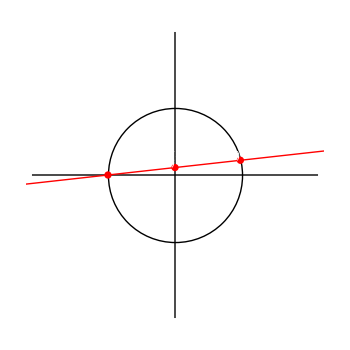
-Graphics-For t=1/9: (RowBox[{)^2 + (RowBox[{)^2 = (RowBox[{)^2

```mathematica
t=1/9;
X=(1-t^2)/(1+t^2);
Y=(2t)/(1+t^2);
Row[{
Graphics[{Line[{(2+1.2t){{-1,0},{1,0}},(2+1.2t){{0,-1},{0,1}}}],Circle[],Red,PointSize[.015],Point[{{-1,0},{0,t},{X,Y}}],InfiniteLine[{{-1,0},{0,t}}],
Inset[Style[StringForm["(0,``)",t],White],{0,t},{Right,Bottom}],Inset[Style[StringForm["(``,``)",X,Y],White],{X,Y},{Right,Bottom}]},ImageSize->350],
Style[StringForm["For t=``: (``)^2 + (``)^2 = (``)^2",t,Numerator@X,Numerator@Y,Denominator@X],20]}]
```

#### t=Y/(X+1), then t ∈ ℚ Y= t(X+1)→(t^2(X+1))^2+X^2=1 →(X+1)((t^2+1)X+t^2-1)=0 We find the roots: X_1=-1→ Y = 0 X_2=(1 - t^2)/(1 + t^2)→Y=(2t)/(1 + t^2) We obtained a BIRRATIONAL EQUIVALENCE/CORRESPONDANCE: Points on circle (with hole) ⇔ Points on y-axis In calculus, we have the Weierstrass substitution:

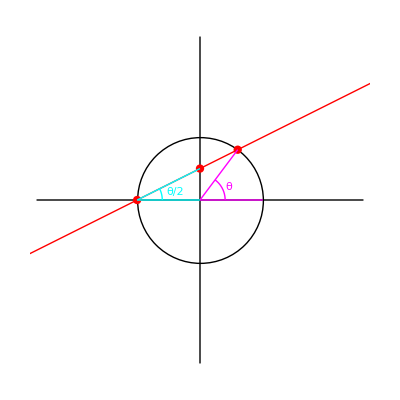

```mathematica
t=1/2;
X=(1-t^2)/(1+t^2);
Y=(2t)/(1+t^2);
Graphics[{Line[{(2+1.2t){{-1,0},{1,0}},(2+1.2t){{0,-1},{0,1}}}],Circle[],Red,PointSize[.015],Point[{{-1,0},{0,t},{X,Y}}],InfiniteLine[{{-1,0},{0,t}}],Magenta,Line[{{{0,0},{X,Y}},{{0,0},{1,0}}}],Circle[{0,0},.4,{0,ArcTan[Y/X]}],Inset["θ",{.45,.2}],
Cyan,Line[{{{-1,0},{0,t}},{{-1,0},{0,0}}}],Circle[{-1,0},.4,{0,ArcTan[Y/X]/2}],Inset["θ/2",{-.4,.13}]},ImageSize->400]
```

#### t=tan(θ/2),X =cos(θ),Y=sin(θ)